# P3327 Mathematica Tutorial Session

## Flip Tanedo, Fall 2012 (7 September 2012)

Rough notes for the Mathematica tutorial session. Rough idea: calculate the potential for a point charge.
Updated 8 September to fix typos.

```mathematica
ClearAll["Global`*"] (* This is just good form *)
```

## Working with “vectors”

Instead of “honest” vectors, we’ll use Mathematica’s lists, which are delimited by curly braces.

```mathematica
testVec1={a,b,c};
testVec2={e,f,g};
```

### Incorrect dot product

```mathematica
testVec1 testVec2
```

{a e,b f,c g}

### Correct dot product

```mathematica
testVec1.testVec2
```

a e+b f+c g

## Potential

The main idea is that we’d like to keep things as modular as possible. We’ll work with the potential from a single point charge at position which is observed at point r. Note that s and r are 3-vectors by assumption.

### Define the potential for a charge q at position s, observed at r

Let q be the charge, s (a vector) be its position, and r (a vector) be the observation point.

```mathematica
PointPhi[q_,s_,r_]:=q/(√((r-s).(r-s)))

(* Note how we entered the denominator! *)
(* ... (s-r)^2 would have given a wrong result! *)
```

```mathematica
(* do a test! *)
PointPhi[q,{sx,sy,sz},{rx,ry,rz}]
```

q/(√((rx-sx)^2+(ry-sy)^2+(rz-sz)^2))

### Now define a function for the desired charge configuration

Consider a charge +2 esu at s1 = (0,0,0) cm and a charge (-1) esu at (1,0,0) cm. (HW2 #6).  You can do this two ways: you can either keep the units explicit (this is useful if you want to later use replacement rules to convert units), or you can do everything unit-less and remember that you’re working in esu and cm.

```mathematica
PhiUnits[x_,y_,z_]:=
PointPhi[2 esu,{0 cm, 0 cm, 0 cm},{x,y,z}]+PointPhi[-1 esu,{1 cm, 0 cm,0 cm},{x,y,z}];

PhiNoUnits[x_,y_,z_]:=PhiUnits[x,y,z]/.{esu->1,cm->1}
```

#### Do a quick sanity check to make sure this makes sense

```mathematica
PhiUnits[x cm,y cm,z cm]
PhiNoUnits[x,y,z]
```

(2 esu)/(√(cm^2 x^2+cm^2 y^2+cm^2 z^2))-esu/(√((-cm+cm x)^2+cm^2 y^2+cm^2 z^2))

-1/(√((-1+x)^2+y^2+z^2))+2/(√(x^2+y^2+z^2))

#### More sanity checks: how to use units

```mathematica
PhiUnits[4 cm, 7 cm, 4 cm]
FullSimplify[% /.esu->1 g^(1/2)cm^(3/2)s^-1,{cm>0}] 
(* second argument tells Mathematica to assume "cm" is positive *)

%/.cm->.01 m
```

(2 esu)/(9 √(cm^2))-esu/(√74 √(cm^2))

((148-9 √74) √(cm g))/(666 s)

(0.0105975 √(g m))/s

## Make some plots

### Contour plot for the equipotential

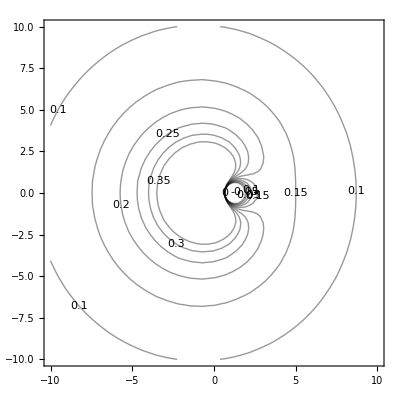

```mathematica
MyContourPlot=ContourPlot[PhiNoUnits[x,0,z],
{x,-10,10},
{z,-10,10},
(*Contours->{0, .1, .2, .3, .5, 1},*)
ContourLabels->All,
ContourShading->None
]
```

### Electric Field

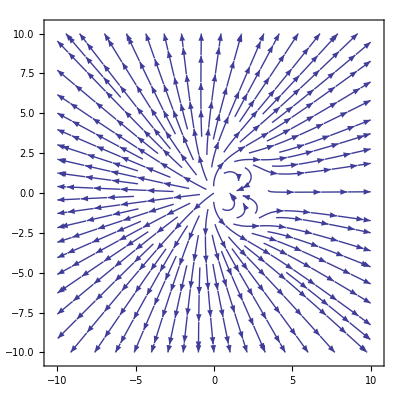

```mathematica
Ex[x_,y_]:=-D[PhiNoUnits[xx,y,0], xx]/.{xx->x}
Ey[x_,y_]:=-D[PhiNoUnits[x,yy,0], yy]/.{yy->y}
EPlot=StreamPlot[{Ex[x,y],Ey[x,y]},{x,-10,10},{y,-10,10}]
```

### Overlay Plots

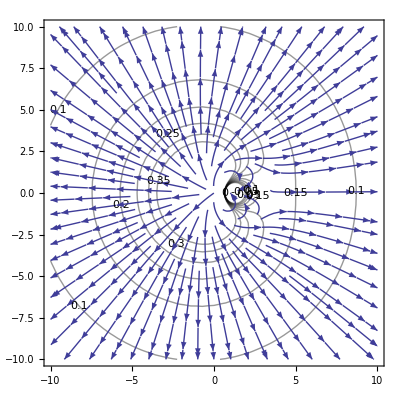

```mathematica
Show[MyContourPlot,EPlot]
```